# Análisis de las unidades de tiempo

```mathematica
SetDirectory[NotebookDirectory[]];
```

## People=100 Capacity=[1-10]

```mathematica
timeVals={1000,10000,100000};
people100=Table[Import[StringJoin["graphs/model-v3/people100/","network-100-",IntegerString[i],"-",IntegerString[timeVals[[j]]],".g6"]],{i,1,10,1},{j,1,3,1}];
```

### Grado de los nodos

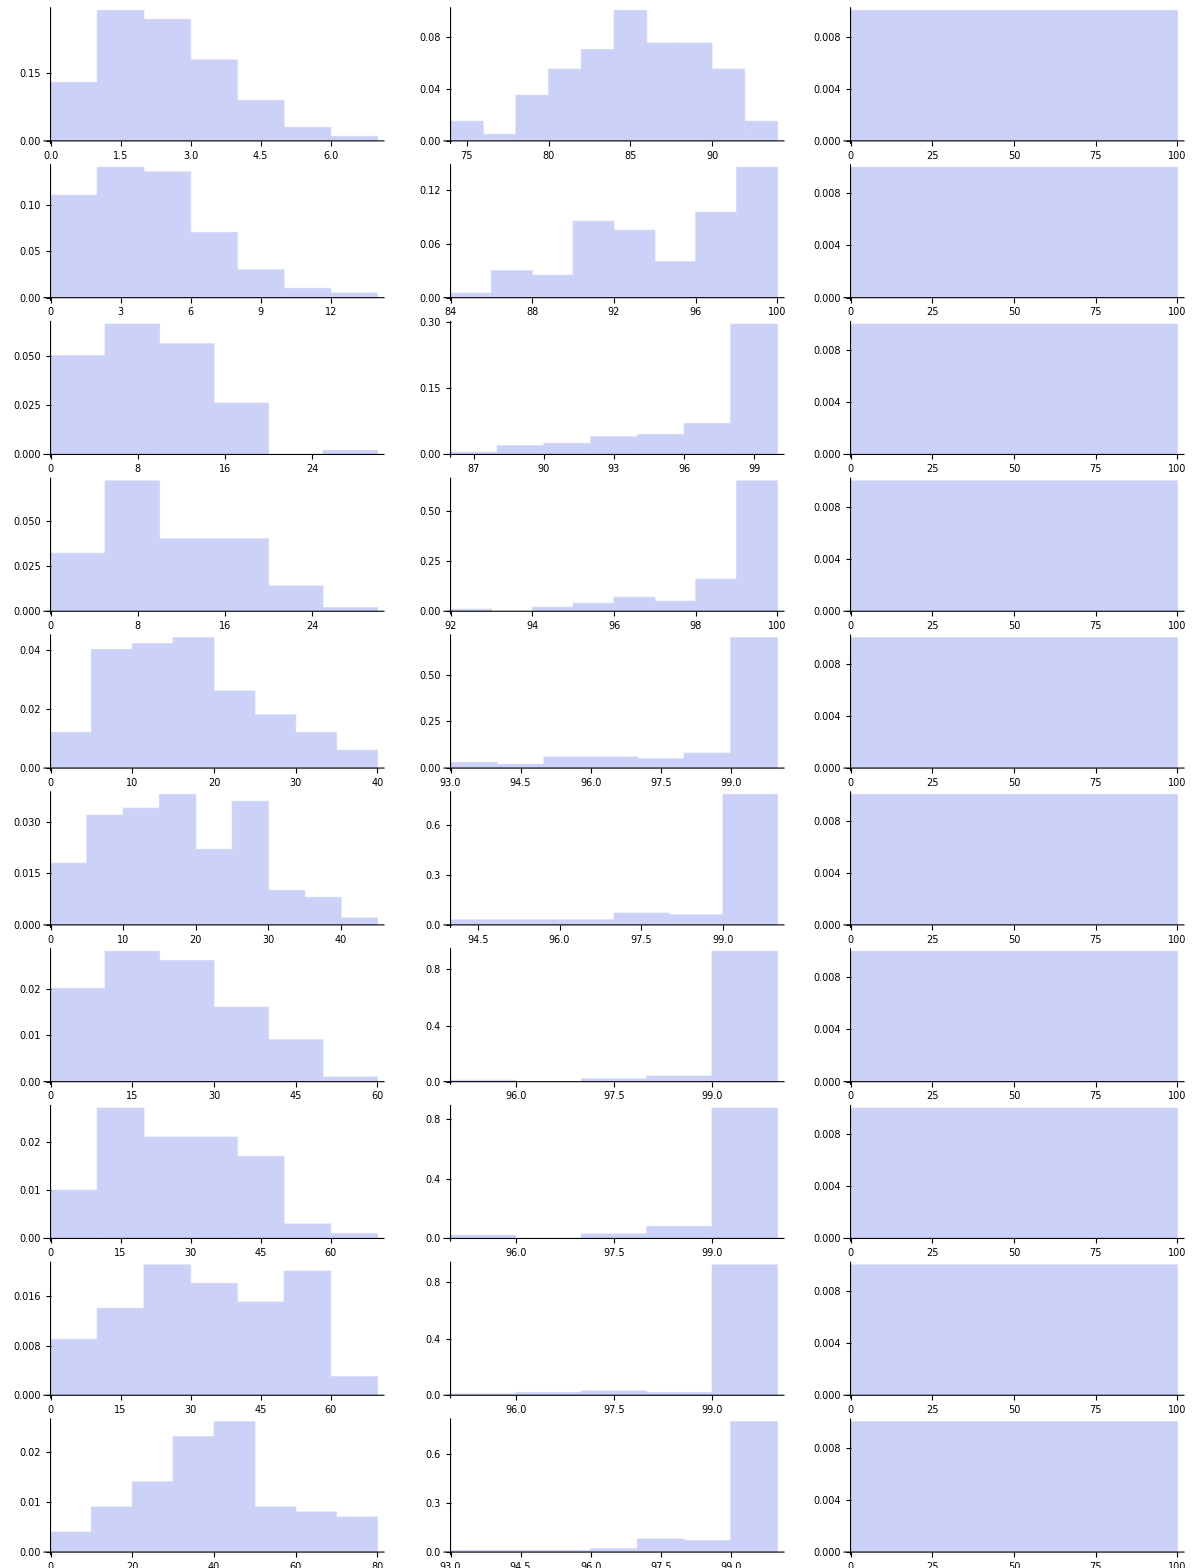

```mathematica
Table[Histogram[VertexDegree[people100[[i,j]]],Automatic,"PDF"],{i,1,Length[people100],1},{j,1,Length[people100[[i]]],1}];
TableForm[%]
```

### Clustering coefficient

```mathematica
clustering100=Map[GlobalClusteringCoefficient,Flatten[people100]];
xy=Table[{i,timeVals[[j]]},{i,1,10,1},{j,1,3,1}];
dataPlotClustering100=Table[Append[Flatten[xy,1][[i]],clustering100[[i]]],{i,1,Length[clustering100],1}];
ListPlot3D[dataPlotClustering100]
```

-Graphics3D-

#### time vs clustering coefficient

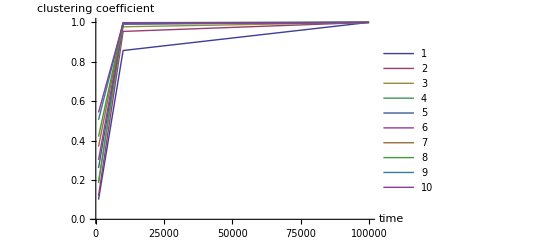

```mathematica
clusteringTime100=Table[Map[GlobalClusteringCoefficient,people100[[i]]],{i,1,Length[people100],1}];
dataPlotClusteringTime100=Table[Table[{timeVals[[j]],clusteringTime100[[i,j]]},{j,1,3,1}],{i,1,10,1}];
ListLinePlot[dataPlotClusteringTime100,PlotLegends->Range[10],AxesLabel->{"time","clustering coefficient"}]
```

#### capacity vs clustering coefficient

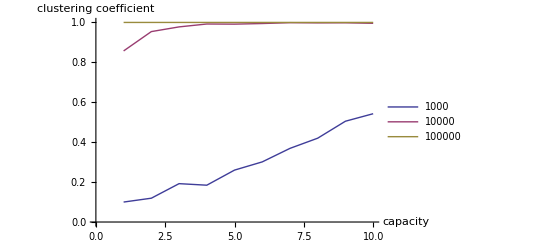

```mathematica
clusteringCap100=Table[Map[GlobalClusteringCoefficient,people100[[i]]],{i,1,Length[people100],1}];
dataPlotClusteringCap100=Table[Table[{i,clusteringTime100[[i,j]]},{i,1,10,1}],{j,1,3,1}];
ListLinePlot[dataPlotClusteringCap100,PlotLegends->timeVals,AxesLabel->{"capacity","clustering coefficient"}]
```

### Average path length

```mathematica
apl100=Map[MeanGraphDistance,Flatten[people100]];
xy=Table[{i,timeVals[[j]]},{i,1,10,1},{j,1,3,1}];
dataPlotApl100=Table[Append[Flatten[xy,1][[i]],apl100[[i]]],{i,1,Length[apl100],1}];
ListPlot3D[dataPlotApl100]
```

-Graphics3D-

#### time vs average path length

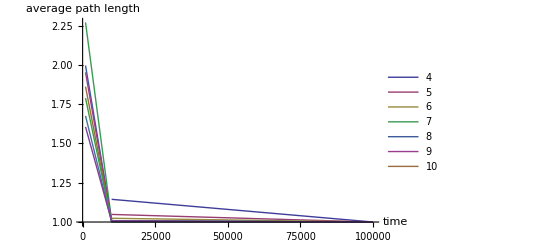

```mathematica
aplTime100=Table[Map[MeanGraphDistance,people100[[i]]],{i,1,Length[people100],1}];
dataPlotAplTime100=Table[Table[{timeVals[[j]],aplTime100[[i,j]]},{j,1,3,1}],{i,1,10,1}];
ListLinePlot[dataPlotAplTime100,PlotLegends->Range[4,10],AxesLabel->{"time","average path length"}]
```

#### capacity vs average path length

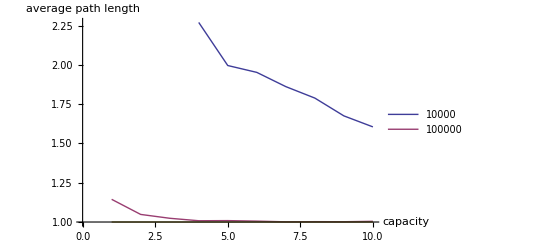

```mathematica
aplCap100=Table[Map[MeanGraphDistance,people100[[i]]],{i,1,Length[people100],1}];
dataPlotAplCap100=Table[Table[{i,aplCap100[[i,j]]},{i,1,10,1}],{j,1,3,1}];
ListLinePlot[dataPlotAplCap100,PlotLegends->{10000,100000},AxesLabel->{"capacity","average path length"}]
```

## People=1000 Capacity=[1-10]

```mathematica
people1000=Table[Import[StringJoin["../graphs/model-v3/people1000/","network-1000-",IntegerString[i],"-",IntegerString[timeVals[[j]]],".g6"]],{i,1,10,1},{j,1,3,1}];
```